## Initialisation

```mathematica
ClearAll["Global`*"]
```

```mathematica
x12 = L1;
x23 = L2;
x13 = L1 + L2;

λ12 = R1 / x12;
λ21 = R2 / x12;
λ23 = R2 / x23;
λ32 = R3 / x23;
λ13 = R1 / x13;
λ31 = R3 / x13;

A11 = A22 = A33 =B11 = B22 = B33 = 1;
A12  = 3/2 λ12;
A13  = 3/2 λ13;
A32  = 3/2 λ32;
A23  = 3/2 λ23;
A21  = 3/2 λ21;
A31  = 3/2 λ31;

B12  = 3/4 λ12;
B13  = 3/4 λ13;
B32  = 3/4 λ32;
B23  = 3/4 λ23;
B21  = 3/4 λ21;
B31  = 3/4 λ31;

mob1 = 1/(6 π μ R1);
mob2 =1/(6 π μ R2);
mob3 = 1/(6 π μ R3);

n = {1, 0, 0};
nn = Outer[Times, n, n];
Imnn = IdentityMatrix[3] - nn;

H11 = mob1 (A11 nn + B11 Imnn);
H22 = mob2 (A22 nn + B22 Imnn);
H33 = mob3 (A33 nn + B33 Imnn);
H12 =mob1 (A12 nn + B12 Imnn);
H13 =mob1 (A13 nn + B13 Imnn);
H23 =mob2 (A23 nn + B23 Imnn);
H21 =mob2 (A21 nn + B21 Imnn);
H32 =mob3 (A32 nn + B32 Imnn);
H31 =mob3 (A31 nn + B31 Imnn);

Fv1 = {f1, 0, 0};
Fv2 = {f2, 0, 0};
Fv3 = {f3, 0, 0};

v1 = (H11.Fv1)[[1]] /. f2 -> -f3 -f1;
v2 = (H22.Fv2)[[1]] /. f2 -> -f3 -f1;
v3 = (H33.Fv3)[[1]] /. f2 -> -f3 -f1;
```

```mathematica
L1dot = v2 - v1 // Simplify;
L2dot = v3 - v2 // Simplify;

Clear[L1DOT, L2DOT]
f3solved =(Solve[L1dot == L1DOT, {f3}] // Flatten)[[1,2]] ;
f1solved = (Solve[L2dot == L2DOT /. f3 -> f3solved, {f1}] // Flatten)[[1,2]];
f3solved = f3solved /. f1-> f1solved;
f2solved = -f1solved - f3solved;

v1solved = v1 /. {f1->f1solved, f3 -> f3solved} ;
v2solved = v2 /. {f1->f1solved, f3 -> f3solved} ;
v3solved = v3 /. {f1->f1solved, f3 -> f3solved} ;
vssolved = 1/3 (v1solved + v2solved + v3solved);
```

```mathematica
L1 = l1 ( 1 + e1 Cos[ω t + ϕ1]);
L2 = l2 ( 1 + e2 Cos[ω t + ϕ2]);
L1DOT = D[L1, t];
L2DOT = D[L2, t];
```

## Non-Dimensionalized

```mathematica
V1 = Collect[v1solved/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω}] ;
V2 = Collect[v2solved/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω}];
V3 = Collect[v3solved/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω}];
VS = Collect[vssolved/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω}] ;
F1 = Collect[f1solved/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω, μ}] ;
F2 = Collect[f2solved/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω, μ}] ;
F3 = Collect[f3solved/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω, μ}] ;
L1star = Collect[L1/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω}] ;
L2star = Collect[L2/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω}] ;
L1DOTstar = Collect[L1DOT/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω}] ;
L2DOTstar = Collect[L2DOT/. {R1 -> R2 r1, R3 -> R2 r3, l1 -> R2 x1, l2-> R2 x2, t-> T/ω} , {R2, ω}] ;
```

## Analysis

```mathematica
X1=1040;
X2=1040;
ratio1 = 2;
ratio3 = 3;
E1 = 0.2;
E2 = 0.2;
omega = 1;
phase1 = π/2;
phase2 = 0;
MainRad2 = 1;
VISC = 1;

Clear[Δs, Δ1, Δ2,Δ3, V1DATA, V2DATA,V3DATA, VSDATA, F1DATA, F2DATA,F3DATA, AJDVS, AJDΔs, avgVS];
avgVS =Table[(1/(2π)NIntegrate[VS /. {r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, 2π}] // Quiet), {T, 0, 2π}];
Δs = Table[ NIntegrate[VS /. {r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ1 = Table[ NIntegrate[V1 /.{r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ2 = Table[ NIntegrate[V2 /. {r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
Δ3 = Table[ NIntegrate[V3 /. {r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, τ}] // Quiet,{τ, 0, 2π, 2π/100}];
V1DATA = Table[ V1 /.{r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, 2π, 2π/100}];
V2DATA = Table[ V2 /. {r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, 2π, 2π/100}];
V3DATA = Table[ V3 /. {r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, 2π, 2π/100}];
VSDATA = Table[ VS /. {r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, 2π, 2π/100}];

F1DATA = Table[ F1 /.{r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, 2π, 2π/100}];
F2DATA = Table[ F2 /.{r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, 2π, 2π/100}];
F3DATA = Table[ F3 /.{r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC}, {T, 0, 2π, 2π/100}];
```

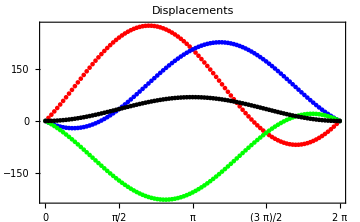
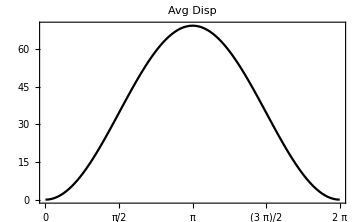
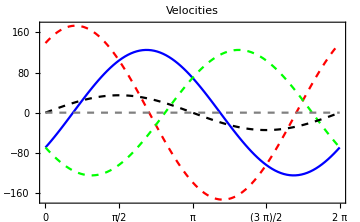
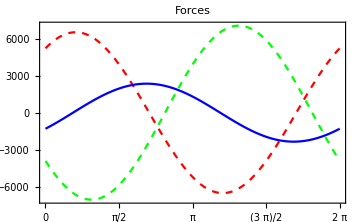
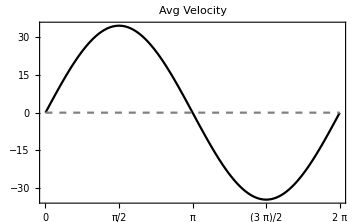
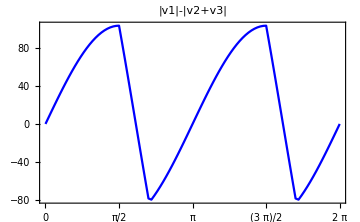
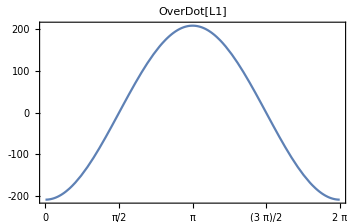
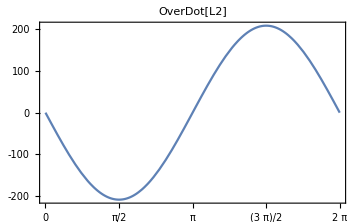

```mathematica
{
Show[ListPlot[Δ1, DataRange->{0, 2π}, PlotStyle-> Red], ListPlot[Δ2, DataRange->{0,2π}, PlotStyle-> Blue],ListPlot[Δ3, DataRange->{0, 2π}, PlotStyle-> Green],ListPlot[Δs, DataRange->{0,2π}, PlotStyle-> Black],
PlotRange-> All, Frame->True,FrameTicks->{{All,None},{{0,Pi/4, Pi/2, 3 Pi/4, Pi, 5Pi/4, 3 Pi/2 , 7 Pi /4, 2Pi},None}},PlotLabel->"Displacements",ImageSize->Medium]
,
Show[
ListLinePlot[Δs, DataRange->{0,2π}, PlotStyle-> Black]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi/4, Pi/2, 3 Pi/4, Pi, 5Pi/4, 3 Pi/2 , 7 Pi /4, 2Pi},None}},PlotLabel->"Avg Disp",ImageSize->Medium]
,
Show[
ListLinePlot[V1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[V2DATA, DataRange->{0,2π}, PlotStyle-> { Blue}]
,
ListLinePlot[V3DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Green}]
,
ListLinePlot[VSDATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Black}]
,
ListLinePlot[avgVS, DataRange->{0,2π}, PlotStyle-> {Dashed, Gray}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi/4, Pi/2, 3 Pi/4, Pi, 5Pi/4, 3 Pi/2 , 7 Pi /4, 2Pi},None}},PlotLabel->"Velocities",ImageSize->Medium, PlotRange -> All]
,
Show[
ListLinePlot[F1DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Red}]
,
ListLinePlot[F2DATA, DataRange->{0,2π}, PlotStyle-> { Blue}]
,
ListLinePlot[F3DATA, DataRange->{0,2π}, PlotStyle-> {Dashed, Green}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi/4, Pi/2, 3 Pi/4, Pi, 5Pi/4, 3 Pi/2 , 7 Pi /4, 2Pi},None}},PlotLabel->"Forces",ImageSize->Medium, PlotRange -> All]
,
Show[
ListLinePlot[VSDATA,DataRange->{0,2π}, PlotStyle-> {Black}]
,
ListLinePlot[avgVS,DataRange->{0,2π}, PlotStyle-> {Dashed, Gray}]
,
Frame->True,FrameTicks->{{All,None},{{0,Pi/4, Pi/2, 3 Pi/4, Pi, 5Pi/4, 3 Pi/2 , 7 Pi /4, 2Pi},None}},ImageSize->Medium,PlotLabel->"Avg Velocity",PlotRange->All]
,
ListLinePlot[{Abs[V1DATA]-Abs[V2DATA+V3DATA]},DataRange->{0,2π},Frame->True,FrameTicks->{{All,None},{{0,Pi/4, Pi/2, 3 Pi/4, Pi, 5Pi/4, 3 Pi/2 , 7 Pi /4, 2Pi},None}},ImageSize->Medium,PlotStyle->{{Blue}},PlotLabel->"|v1|-|v2+v3|"]
,
Plot[L1DOTstar/. {r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC},{T,0,2π},ImageSize->Medium,PlotLabel->"OverDot[L1]",Frame->True,FrameTicks->{{All,None},{{0,Pi/4, Pi/2, 3 Pi/4, Pi, 5Pi/4, 3 Pi/2 , 7 Pi /4, 2Pi},None}}]
,
Plot[L2DOTstar/. {r1-> ratio1, r3-> ratio3, x1-> X1, x2->X2, e1-> E1, e2-> E2, ω->omega, ϕ2-> phase2, ϕ1-> phase1, R2->MainRad2,μ->VISC},{T,0,2π},ImageSize->Medium,PlotLabel->"OverDot[L2]",Frame->True,FrameTicks->{{All,None},{{0,Pi/4, Pi/2, 3 Pi/4, Pi, 5Pi/4, 3 Pi/2 , 7 Pi /4, 2Pi},None}}]
}
```